```mathematica
e[v_, r_]:= v^2 r+1;
alpha[e_]:=2ArcTan[√(e^2-1)];
Plot[Pi -alpha[e[v]],{v,0,1}]
Plot[e[v],{v,0,1}]
```

-Graphics-

-Graphics-

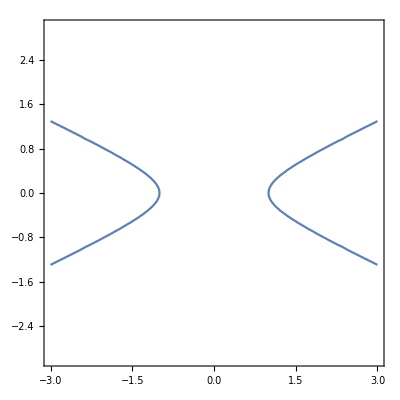

```mathematica
a=1;
ContourPlot[x^2/a^2-y^2/(a^2(1.1^2-1))==1,{x,-3,3},{y,-3,3}]
```

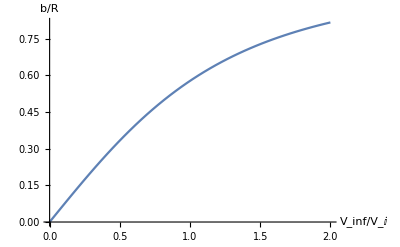

```mathematica
Plot[1/(√(1+2 v^-2)),{v,0,2},AxesLabel->{Subscript[V, inf] / Subscript[V, I],b/R}]
```

```mathematica
Plot[Pi -alpha[e[v]],{v,0,1},AxesLabel->{Subscript[V, inf] / Subscript[V, I],α}]
```

-Graphics-

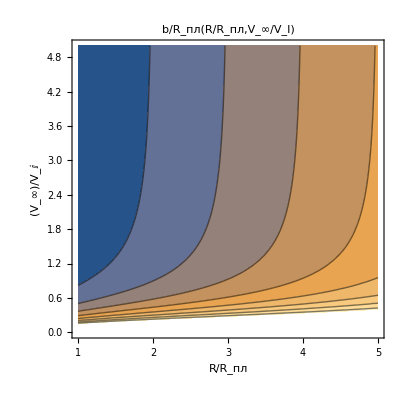

```mathematica
ContourPlot[{√(r^2+(2 r)/v^2)},{r,1,5},{v,0,5}, AxesLabel->{R/Subscript[R, пл],Subscript[V, ∞]/Subscript[V, I]}, PlotLabel->"b/R_(:043f:043b)(R/R_(:043f:043b),V_∞/V_I)"]
```

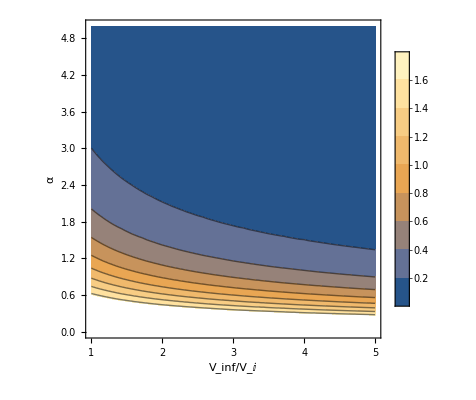

```mathematica
ContourPlot[Pi -alpha[e[v,r]],{r,1,5},{v,0,5},FrameLabel->{Subscript[V, inf] / Subscript[V, I],α}, PlotLegends->Automatic]
```

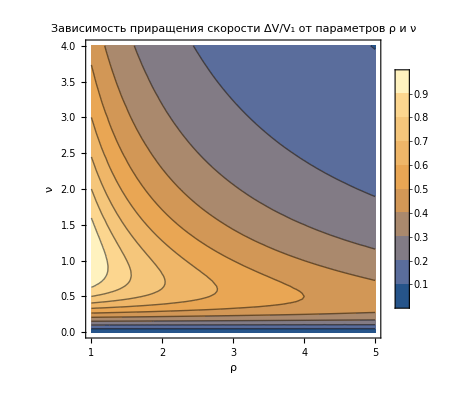

```mathematica
ContourPlot[v √(2(1+ Cos[alpha[e[v,r]]])),{r,1,5},{v,0,4},FrameLabel->{ρ,ν}, PlotLegends->Automatic, PlotLabel->"Зависимость приращения скорости ΔV/V_1 от параметров ρ и ν"]
```

```mathematica
Simplify[Grad[v √(2(1+ Cos[alpha[e[v,r]]])),{v,r}]]
Simplify[D[v √(2(1+ Cos[alpha[e[v,r]]])),v]]
```

{-(2 (-1+r v^2) √(1/((1+r v^2)^2)))/(1+r v^2),-(v^3 Sin[2 ArcTan[√(r v^2 (2+r v^2))]])/(√(1/((1+r v^2)^2)) (1+r v^2) √(r v^2 (2+r v^2)))}

-(2 (-1+r v^2) √(1/((1+r v^2)^2)))/(1+r v^2)

```mathematica
{-(2 (-1+r v^2) √(1/((1+r v^2)^2)))/(1+r v^2),-(v^3 Sin[2 ArcTan[√(r v^2 (2+r v^2))]])/(√(1/((1+r v^2)^2)) (1+r v^2) √(r v^2 (2+r v^2)))}
```

√2 √(1+Cos[2 ArcTan[√(-1+(1+r v^2)^2)]])-(2 √2 r v^2 Sin[2 ArcTan[√(-1+(1+r v^2)^2)]])/((1+r v^2) √(-1+(1+r v^2)^2) √(1+Cos[2 ArcTan[√(-1+(1+r v^2)^2)]]))

```mathematica
FindMaximum[√(v^2 2  (1+ Cos[alpha[e[v,r]]]))&& r ≥1 && v > 0,{r,v}]
```

FindMaximum::nrnum: The function value -False is not a real number at {r,v} = {0.646447,1.}.

{1.,{r→1.,v→1.}}

```mathematica
ContourPlot[v √(2(1 + Cos[2 ArcTan[√((r v^2 + 1)^2-1)]])),{r,1,5},{v,0,4},FrameLabel->{ρ,ν}, PlotLegends->Automatic, PlotLabel->"Зависимость приращения скорости ΔV/V_1 от параметров ρ и ν"]
```

-Graphics-

```mathematica
N[ArcTan[Sqrt[3]]*180/Pi]
```

60.

```mathematica
v √(2(1+ Cos[alpha[e[v,r]]]))
```

√2 v √(1+Cos[2 ArcTan[√(-1+(1+r v^2)^2)]])

```mathematica
data=Flatten[Table[Join[Table[{SetPrecision[r,3], SetPrecision[v,3],SetPrecision[v √(2(1+ Cos[alpha[e[v,r]]])),3]},{r,1,5,0.2}],{{}}],{v,0,4,0.2}],1];
Export[FileNameJoin[{NotebookDirectory[],"..","data","grav-assist.txt"}],
Join[{{"r","v","D"}},data],"Table"]
```

/Users/ashepelev/astro/astro.notebook/astro.notebook.third/calc/../data/grav-assist.txt

```mathematica
data
```

{{1.,0,0},{1.3,0,0},{1.6,0,0},{1.9,0,0},{2.2,0,0},{2.5,0,0},{2.8,0,0},{3.1,0,0},{3.4,0,0},{3.7,0,0},{4.,0,0},{4.3,0,0},{4.6,0,0},{4.9,0,0},{},{1.,0.3,0.55},{1.3,0.3,0.537},{1.6,0.3,0.524},{1.9,0.3,0.512},{2.2,0.3,0.501},{2.5,0.3,0.49},{2.8,0.3,0.479},{3.1,0.3,0.469},{3.4,0.3,0.459},{3.7,0.3,0.45},{4.,0.3,0.441},{4.3,0.3,0.433},{4.6,0.3,0.424},{4.9,0.3,0.416},{},{1.,0.6,0.882},{1.3,0.6,0.817},{1.6,0.6,0.761},{1.9,0.6,0.713},{2.2,0.6,0.67},{2.5,0.6,0.632},{2.8,0.6,0.598},{3.1,0.6,0.567},{3.4,0.6,0.54},{3.7,0.6,0.515},{4.,0.6,0.492},{4.3,0.6,0.471},{4.6,0.6,0.452},{4.9,0.6,0.434},{},{1.,0.9,0.994},{1.3,0.9,0.877},{1.6,0.9,0.784},{1.9,0.9,0.709},{2.2,0.9,0.647},{2.5,0.9,0.595},{2.8,0.9,0.551},{3.1,0.9,0.513},{3.4,0.9,0.479},{3.7,0.9,0.45},{4.,0.9,0.425},{4.3,0.9,0.402},{4.6,0.9,0.381},{4.9,0.9,0.362},{},{1.,1.2,0.984},{1.3,1.2,0.836},{1.6,1.2,0.726},{1.9,1.2,0.642},{2.2,1.2,0.576},{2.5,1.2,0.522},{2.8,1.2,0.477},{3.1,1.2,0.439},{3.4,1.2,0.407},{3.7,1.2,0.379},{4.,1.2,0.355},{4.3,1.2,0.334},{4.6,1.2,0.315},{4.9,1.2,0.298},{},{1.,1.5,0.923},{1.3,1.5,0.764},{1.6,1.5,0.652},{1.9,1.5,0.569},{2.2,1.5,0.504},{2.5,1.5,0.453},{2.8,1.5,0.411},{3.1,1.5,0.376},{3.4,1.5,0.347},{3.7,1.5,0.322},{4.,1.5,0.3},{4.3,1.5,0.281},{4.6,1.5,0.264},{4.9,1.5,0.249},{},{1.,1.8,0.849},{1.3,1.8,0.691},{1.6,1.8,0.582},{1.9,1.8,0.503},{2.2,1.8,0.443},{2.5,1.8,0.396},{2.8,1.8,0.357},{3.1,1.8,0.326},{3.4,1.8,0.3},{3.7,1.8,0.277},{4.,1.8,0.258},{4.3,1.8,0.241},{4.6,1.8,0.226},{4.9,1.8,0.213},{},{1.,2.1,0.776},{1.3,2.1,0.624},{1.6,2.1,0.521},{1.9,2.1,0.448},{2.2,2.1,0.392},{2.5,2.1,0.349},{2.8,2.1,0.315},{3.1,2.1,0.286},{3.4,2.1,0.263},{3.7,2.1,0.243},{4.,2.1,0.225},{4.3,2.1,0.21},{4.6,2.1,0.197},{4.9,2.1,0.186},{},{1.,2.4,0.71},{1.3,2.4,0.566},{1.6,2.4,0.47},{1.9,2.4,0.402},{2.2,2.4,0.351},{2.5,2.4,0.312},{2.8,2.4,0.28},{3.1,2.4,0.255},{3.4,2.4,0.233},{3.7,2.4,0.215},{4.,2.4,0.2},{4.3,2.4,0.186},{4.6,2.4,0.175},{4.9,2.4,0.164},{},{1.,2.7,0.651},{1.3,2.7,0.515},{1.6,2.7,0.426},{1.9,2.7,0.364},{2.2,2.7,0.317},{2.5,2.7,0.281},{2.8,2.7,0.252},{3.1,2.7,0.229},{3.4,2.7,0.209},{3.7,2.7,0.193},{4.,2.7,0.179},{4.3,2.7,0.167},{4.6,2.7,0.156},{4.9,2.7,0.147},{},{1.,3.,0.6},{1.3,3.,0.472},{1.6,3.,0.39},{1.9,3.,0.331},{2.2,3.,0.288},{2.5,3.,0.255},{2.8,3.,0.229},{3.1,3.,0.208},{3.4,3.,0.19},{3.7,3.,0.175},{4.,3.,0.162},{4.3,3.,0.151},{4.6,3.,0.142},{4.9,3.,0.133},{},{1.,3.3,0.555},{1.3,3.3,0.435},{1.6,3.3,0.358},{1.9,3.3,0.304},{2.2,3.3,0.264},{2.5,3.3,0.234},{2.8,3.3,0.21},{3.1,3.3,0.19},{3.4,3.3,0.174},{3.7,3.3,0.16},{4.,3.3,0.148},{4.3,3.3,0.138},{4.6,3.3,0.129},{4.9,3.3,0.121},{},{1.,3.6,0.516},{1.3,3.6,0.403},{1.6,3.6,0.331},{1.9,3.6,0.281},{2.2,3.6,0.244},{2.5,3.6,0.216},{2.8,3.6,0.193},{3.1,3.6,0.175},{3.4,3.6,0.16},{3.7,3.6,0.147},{4.,3.6,0.136},{4.3,3.6,0.127},{4.6,3.6,0.119},{4.9,3.6,0.112},{},{1.,3.9,0.481},{1.3,3.9,0.375},{1.6,3.9,0.308},{1.9,3.9,0.261},{2.2,3.9,0.226},{2.5,3.9,0.2},{2.8,3.9,0.179},{3.1,3.9,0.162},{3.4,3.9,0.148},{3.7,3.9,0.136},{4.,3.9,0.126},{4.3,3.9,0.117},{4.6,3.9,0.11},{4.9,3.9,0.103},{}}